# Monte Carlo evaluation

```mathematica
corr[{n1_,m1_},{n2_,m2_},τ_:τ]:=If[EvenQ[n1+n2]∧EvenQ[m1+m2],((-1)^(n1+m1)ⅈ^(n1+m1+n2+m2)Subscript[τ, 1/2(n1+m1+n2+m2)]^2)/(2π)(2Gamma[1/2(1+n1+n2)]Gamma[1/2(1+m1+m2)])/Gamma[1+1/2(n1+m1+n2+m2)],0]
p[Y_,M_]:=Exp[-1/2 Y.Inverse[M].Y]/(√((2π)^Length[M] Det[M]))
pre[M_]:=1/(√((2π)^Length[M] Det[M]))

Cov[correlations_,τ_:τ]:=Table[corr[i,j,τ],{i,correlations},{j,correlations}]
```

## Critical points

```mathematica
Nsamples=1000000;
moments=Join[{Subscript[σ, 0]->7.2588,Subscript[σ, 1]->40.974,Subscript[σ, 2]->285.905,Subscript[σ, 3]->2269.1},{Subscript[τ, 0]->1,Subscript[τ, 1]->1.76201,Subscript[τ, 2]->7.02844,Subscript[τ, 3]->40.1639,Subscript[τ, 4]->281.132,Subscript[τ, 5]->2257.73}];
range=30;
```

## Critical δ

### Critical points δ method 0

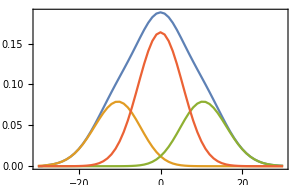

```mathematica
numberDensities0=ParallelTable[
{Quiet[NIntegrate[π(δ11-δ22)Abs[δ11 δ22]p[{δ,0,0,δ11,0,δ22},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}},σ]]/.moments,{δ11,-∞,∞},{δ22,-∞,δ11}]],
Quiet[NIntegrate[π(δ11-δ22)Abs[δ11 δ22]p[{δ,0,0,δ11,0,δ22},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}},σ]]/.moments,{δ11,0,∞},{δ22,0,δ11}]],
Quiet[NIntegrate[π(δ11-δ22)Abs[δ11 δ22]p[{δ,0,0,δ11,0,δ22},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}},σ]]/.moments,{δ11,-∞,0},{δ22,-∞,δ11}]],
Quiet[NIntegrate[π(δ11-δ22)Abs[δ11 δ22]p[{δ,0,0,δ11,0,δ22},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}},σ]]/.moments,{δ11,0,∞},{δ22,-∞,0}]]}
,{δ,-range,range}]ᵀ;
ListLinePlot[numberDensities0,DataRange->{-range,range},Frame->True,ImageSize->300]
```

### Critical points δ method 1

```mathematica
Simplify[Abs[δ11 δ22-δ12^2] p[{δ,0,0,δ11,δ12,δ22},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}},σ]]/p[{δ11,δ12,δ22},Cov[{{2,0},{1,1},{0,2}},σ]],Assumptions->{Subscript[σ, 0]>0,Subscript[σ, 1]>0,Subscript[σ, 2]>0,Subscript[σ, 3]>0}]
```

(ⅇ^(-(((δ11+δ22) σ_1^2+δ σ_2^2)^2)/(-2 σ_1^4 σ_2^2+2 σ_0^2 σ_2^4)) Abs[δ12^2-δ11 δ22] σ_2^3)/(π^(3/2) √(-2 σ_1^8 σ_2^4+2 σ_0^2 σ_1^4 σ_2^6))

```mathematica
Module[{arg,det,trace,random,randomArg,randomDet,randomTrace},
arg=With[{tmp=Simplify[Abs[δ11 δ22-δ12^2] p[{δ,0,0,δ11,δ12,δ22},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}},σ]]/p[{δ11,δ12,δ22},Cov[{{2,0},{1,1},{0,2}},σ]],Assumptions->{Subscript[σ, 0]>0,Subscript[σ, 1]>0,Subscript[σ, 2]>0,Subscript[σ, 3]>0}]/.moments},
Compile[{{δ,_Real},{δ11,_Real},{δ12,_Real},{δ22,_Real}},tmp]];
det=Compile[{{δ11,_Real},{δ12,_Real},{δ22,_Real}},HeavisideTheta[δ11 δ22-δ12^2]];
trace=Compile[{{δ11,_Real},{δ12,_Real},{δ22,_Real}},HeavisideTheta[δ11 +δ22]];

random=RandomVariate[MultinormalDistribution[Cov[{{2,0},{1,1},{0,2}},σ]/.moments],Nsamples];
randomDet=ParallelMap[det[#⟦1⟧,#⟦2⟧,#⟦3⟧]&,random];
randomTrace=ParallelMap[trace[#⟦1⟧,#⟦2⟧,#⟦3⟧]&,random];
Monitor[numberDensities1=Table[
randomArg=ParallelMap[arg[δ,#⟦1⟧,#⟦2⟧,#⟦3⟧]&,random];
{Mean[randomArg],Mean[randomArg randomDet randomTrace],Mean[randomArg randomDet (1-randomTrace)],Mean[randomArg (1-randomDet)]}
,{δ,-range,range,1/2}]ᵀ;,N[δ]]]
Beep[]
```

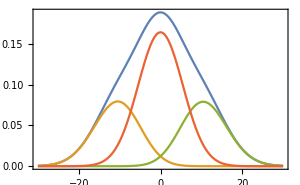

```mathematica
ListLinePlot[numberDensities1,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

### Critical points δ method 2

```mathematica
Simplify[π(δ11-δ22)Abs[δ11 δ22] p[{δ,0,0,δ11,0,δ22},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}},σ]]/p[{δ11,δ22},Cov[{{2,0},{0,2}},σ]],Assumptions->{Subscript[σ, 0]>0,Subscript[σ, 1]>0,Subscript[σ, 2]>0,Subscript[σ, 3]>0}]
```

(√2 ⅇ^(-(((δ11+δ22) σ_1^2+δ σ_2^2)^2)/(-2 σ_1^4 σ_2^2+2 σ_0^2 σ_2^4)) (δ11-δ22) Abs[δ11 δ22])/(π σ_1^2 √(-σ_1^4+σ_0^2 σ_2^2))

```mathematica
Module[{arg,det,trace,random,randomArg,randomDet,randomTrace},
arg=With[{tmp=Simplify[π (δ11-δ22)Abs[δ11 δ22](p[{δ,0,0,δ11,0,δ22},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2}},σ]]/p[{δ11,δ22},Cov[{{2,0},{0,2}},σ]]),Assumptions->{Subscript[σ, 0]>0,Subscript[σ, 1]>0,Subscript[σ, 2]>0,Subscript[σ, 3]>0}]/.moments},
Compile[{{δ,_Real},{δ11,_Real},{δ22,_Real}},HeavisideTheta[δ11-δ22]tmp]];
det=Compile[{{δ11,_Real},{δ22,_Real}},HeavisideTheta[δ11 δ22]];
trace=Compile[{{δ11,_Real},{δ22,_Real}},HeavisideTheta[δ11 +δ22]];

random=RandomVariate[MultinormalDistribution[Cov[{{2,0},{0,2}},σ]/.moments],Nsamples];
randomDet=ParallelMap[det[#⟦1⟧,#⟦2⟧]&,random];
randomTrace=ParallelMap[trace[#⟦1⟧,#⟦2⟧]&,random];
Monitor[numberDensities2=Table[
randomArg=ParallelMap[arg[δ,#⟦1⟧,#⟦2⟧]&,random];
{Mean[randomArg],Mean[randomArg randomDet randomTrace],Mean[randomArg randomDet (1-randomTrace)],Mean[randomArg (1-randomDet)]}
,{δ,-range,range,1/2}]ᵀ;,N[δ]]]
Beep[]
```

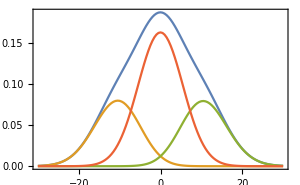

```mathematica
ListLinePlot[numberDensities2,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

### Comparison of the three integration methods

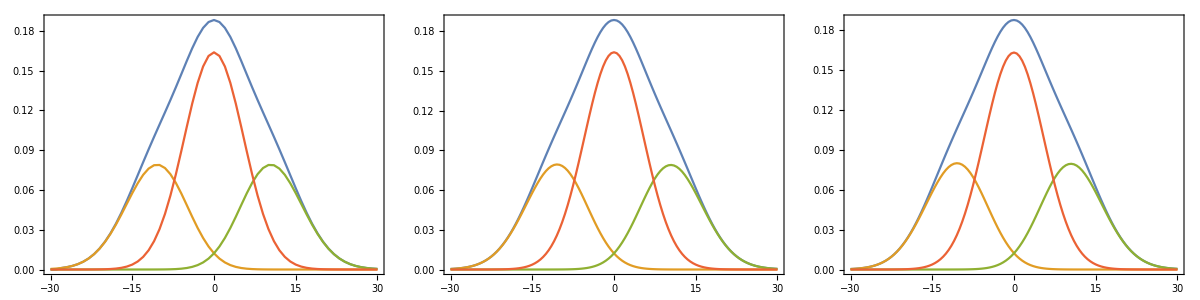

```mathematica
Grid[{{
ListLinePlot[numberDensities0,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All],
ListLinePlot[numberDensities1,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All],
ListLinePlot[numberDensities2,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
}}]
```

## Critical λ

```mathematica
Simplify[π(λ-T22)Abs[T1111(T1122+(2 T122^2)/(λ-T22))-T1112^2] p[{λ,0,T22,0,0,T122,T1111,T1112,T1122},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{2,2}},τ]]/p[{T22,T122,T1111,T1112,T1122},Cov[{{0,2},{1,2},{4,0},{3,1},{2,2}},τ]],Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]
```

-1/(π τ_3^3 √(-8 τ_3^12+38 τ_2^2 τ_3^8 τ_4^2-55 τ_2^4 τ_3^4 τ_4^4+25 τ_2^6 τ_4^6))4 ⅇ^(-(-256 (5 T1111^2+28 T1112^2-10 T1111 T1122+5 T1122^2) τ_3^18+160 (7 T122^2+2 (T1111-T1122) (5 T22-7 λ)) τ_3^16 τ_4^2-40 (193 T122^2+170 T1111 T22-90 T1122 T22-302 T1111 λ+190 T1122 λ) τ_2^2 τ_3^12 τ_4^4+100 (191 T122^2+92 T1111 T22-20 T1122 T22-212 T1111 λ+60 T1122 λ) τ_2^4 τ_3^8 τ_4^6-4000 (5 T122^2+T1111 (T22-3 λ)) τ_2^6 τ_3^4 τ_4^8+7500 T122^2 τ_2^8 τ_4^10+625 (T22-3 λ)^2 τ_2^6 τ_3^2 τ_4^10+4 τ_3^14 (16 (105 T1111^2+632 T1112^2-130 T1111 T1122+25 T1122^2) τ_2^2 τ_4^2-5 (5 T22-7 λ)^2 τ_4^4)-5 τ_3^10 (256 (9 T1111^2+56 T1112^2-5 T1111 T1122) τ_2^4 τ_4^4-5 (65 T22^2-246 T22 λ+217 λ^2) τ_2^2 τ_4^6)+50 τ_3^6 (128 (T1111^2+6 T1112^2) τ_2^6 τ_4^6-5 (7 T22^2-34 T22 λ+39 λ^2) τ_2^4 τ_4^8))/(10 τ_3^2 τ_4^2 (7 τ_3^4-15 τ_2^2 τ_4^2) (2 τ_3^4-5 τ_2^2 τ_4^2) (4 τ_3^4-5 τ_2^2 τ_4^2) (τ_3^4-τ_2^2 τ_4^2))) (T22-λ) Abs[T1112^2-T1111 (T1122+(2 T122^2)/(-T22+λ))] √(-70 τ_3^6 τ_4^4+150 τ_2^2 τ_3^2 τ_4^6)

```mathematica
Module[{arg,det,trace,random,randomArg,randomDet,randomTrace},arg=With[{tmp=Simplify[π(T11-T22)Abs[T1111(T1122+(2 T122^2)/(λ-T22))-T1112^2] p[{T11,0,T22,0,0,T122,T1111,T1112,T1122},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{2,2}},τ]]/p[{T22,T122,T1111,T1112,T1122},Cov[{{0,2},{1,2},{4,0},{3,1},{2,2}},τ]],Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]/.moments},
Compile[{{T11,_Real},{T22,_Real},{T122,_Real},{T1111,_Real},{T1112,_Real},{T1122,_Real}},HeavisideTheta[T11-T22]tmp]];
det=Compile[{{T11,_Real},{T22,_Real},{T122,_Real},{T1111,_Real},{T1112,_Real},{T1122,_Real}},HeavisideTheta[T1111(T1122+(2 T122^2)/(T11-T22))-T1112^2]];
trace=Compile[{{T11,_Real},{T22,_Real},{T122,_Real},{T1111,_Real},{T1112,_Real},{T1122,_Real}},HeavisideTheta[T1111 +T1122+(2 T122^2)/(T11-T22)]];

random=RandomVariate[MultinormalDistribution[Cov[{{0,2},{1,2},{4,0},{3,1},{2,2}},τ]/.moments],Nsamples];
Monitor[numberDensities=Table[
randomArg=ParallelMap[arg[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random];
randomDet=ParallelMap[det[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random];
randomTrace=ParallelMap[trace[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random];
{Mean[randomArg],Mean[randomArg randomDet randomTrace],Mean[randomArg randomDet (1-randomTrace)],Mean[randomArg (1-randomDet)]}
,{λ,-range,range,1/2}]ᵀ;,N[λ]]]
Beep[]
```

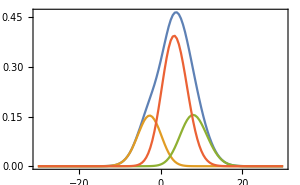

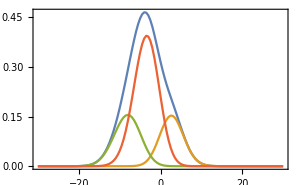

```mathematica
ListLinePlot[numberDensities,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
ListLinePlot[numberDensities⟦All,-1;;1;;-1⟧,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

## Caustics

### A_2 fold curve

```mathematica
Simplify[π(T11-T22)√(T111^2+T112^2)p[{T11,0,T22,T111,T112},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1}},τ]]/p[{T22,T111,T112},Cov[{{0,2},{3,0},{2,1}},τ]],Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]
```

(√6 ⅇ^(-(-3 T11+T22)^2/(6 τ_2^2)) √(T111^2+T112^2) (T11-T22))/τ_2^2

```mathematica
Module[{arg,det,random,randomArg,randomDet},
arg=With[{tmp=Simplify[π(T11-T22)√(T111^2+T112^2)p[{T11,0,T22,T111,T112},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1}},τ]]/p[{T22,T111,T112},Cov[{{0,2},{3,0},{2,1}},τ]],Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]/.moments},
Compile[{{T11,_Real},{T22,_Real},{T111,_Real},{T112,_Real}},HeavisideTheta[T11-T22]tmp]];

random=RandomVariate[MultinormalDistribution[Cov[{{0,2},{3,0},{2,1}},τ]/.moments],Nsamples];
Monitor[A2Length1=Table[Mean[ParallelMap[arg[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧]&,random]],{λ,-range,range,1/2}];,N[λ]]]
Beep[]
```

```mathematica
(*Module[{arg,det,random,randomArg,randomDet},
arg=With[{tmp=Simplify[π(T11-T22)√(T122^2+T222^2)p[{T11,0,T22,T122,T222},Cov[{{2,0},{1,1},{0,2},{1,2},{0,3}},τ]]/p[{T11,T122,T222},Cov[{{2,0},{1,2},{0,3}},τ]],Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]/.moments},
Compile[{{T11,_Real},{T22,_Real},{T122,_Real},{T222,_Real}},HeavisideTheta[T11-T22]tmp]];

random=RandomVariate[MultinormalDistribution[Cov[{{2,0},{1,2},{0,3}},τ]/.moments],Nsamples];
Monitor[A2Length2=Table[Mean[ParallelMap[arg[#⟦1⟧,λ,#⟦2⟧,#⟦3⟧]&,random]],{λ,-40,40,1/2}];,N[λ]]]
Beep[]*)
```

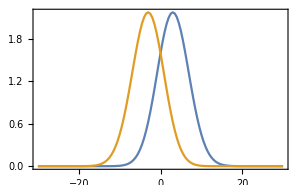

```mathematica
ListLinePlot[{A2Length1,A2Length1⟦-1;;1;;-1⟧},DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

### A_3 cusp curve

```mathematica
Simplify[π(T11-T22)√((T1111+(3 T112^2)/(T11-T22))^2+(T1112+(3T112 T122)/(T11-T22))^2)(p[{T11,0,T22,0,T112,T122,T1111,T1112},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1}},τ]]/p[{T22,T112,T122,T1111,T1112},Cov[{{0,2},{2,1},{1,2},{4,0},{3,1}},τ]]),Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]
```

1/(τ_2 τ_3 √(136 τ_3^8-310 τ_2^2 τ_3^4 τ_4^2+175 τ_2^4 τ_4^4))2 ⅇ^(-(-320 (T11-5 T22)^2 τ_3^14 τ_4^2+367500 T122^2 τ_2^8 τ_4^8-20 τ_2^4 τ_3^6 τ_4^2 (1792 (7 T1111^2+53 T1112^2) τ_3^4+160 (154 T11 T1111-97 T122^2-84 T1111 T22) τ_3^2 τ_4^2+175 (69 T11^2-74 T11 T22+17 T22^2) τ_4^4)+16 τ_2^2 τ_3^10 (4352 T1112^2 τ_3^4+40 (28 T11 T1111-17 T122^2-140 T1111 T22) τ_3^2 τ_4^2+25 (43 T11^2-234 T11 T22+95 T22^2) τ_4^4)+175 τ_2^6 (1792 (T1111^2+6 T1112^2) τ_3^6 τ_4^4+40 (84 T11 T1111-95 T122^2-28 T1111 T22) τ_3^4 τ_4^6+175 (-3 T11+T22)^2 τ_3^2 τ_4^8))/(10 τ_2^2 τ_3^2 τ_4^2 (-4 τ_3^4+5 τ_2^2 τ_4^2) (-34 τ_3^4+35 τ_2^2 τ_4^2) (-4 τ_3^4+105 τ_2^2 τ_4^2))) √(5/π) √((T1111+(3 T112^2)/(T11-T22))^2+(T1112+(3 T112 T122)/(T11-T22))^2) (T11-T22) τ_4 √(-4 τ_3^4+105 τ_2^2 τ_4^2)

```mathematica
Module[{arg,det,random,randomArg,randomDet},
arg=With[{tmp=Simplify[π(T11-T22)√((T1111+(3 T112^2)/(T11-T22))^2+(T1112+(3T112 T122)/(T11-T22))^2)(p[{T11,0,T22,0,T112,T122,T1111,T1112},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1}},τ]]/p[{T22,T112,T122,T1111,T1112},Cov[{{0,2},{2,1},{1,2},{4,0},{3,1}},τ]]),Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]/.moments},
Compile[{{T11,_Real},{T22,_Real},{T112,_Real},{T122,_Real},{T1111,_Real},{T1112,_Real}},HeavisideTheta[T11-T22]tmp]];

random=RandomVariate[MultinormalDistribution[Cov[{{0,2},{2,1},{1,2},{4,0},{3,1}},τ]/.moments],Nsamples];
Monitor[A3Length=Table[Mean[ParallelMap[arg[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random]],{λ,-range,range,1/2}];,N[λ]]]
Beep[]
```

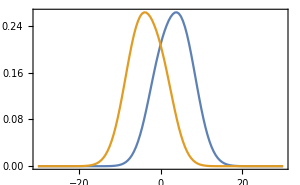

```mathematica
ListLinePlot[{A3Length,A3Length⟦-1;;1;;-1⟧},DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

### A_3 Morse points

```mathematica
Simplify[(π(T11-T22))/Abs[T112] Abs[-1/(T11-T22)^3 T112 (T11 T1112+3 T112 T122-T1112 T22) (T11^2 T11111+10 T11 T1112 T112+15 T112^2 T122-2 (T11 T11111+5 T1112 T112) T22+T11111 T22^2)](p[{T11,0,T22,0,T112,T122,-(3 T112^2)/(T11-T22),T1112,T11111},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{5,0}},τ]]/p[{T22,T112,T122,T1112,T11111},Cov[{{0,2},{2,1},{1,2},{3,1},{5,0}},τ]]),Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]
```

-((8 ⅇ^((4 T22^2)/(3 τ_2^2)+(2 (T11-5 T22)^2 τ_3^4)/(-34 τ_2^2 τ_3^4+35 τ_2^4 τ_4^2)+64 τ_2^2 ((9 T112^4)/((T11-T22)^2 (34 τ_3^4-35 τ_2^2 τ_4^2))+T1112^2/(4 τ_3^4-5 τ_2^2 τ_4^2))+(1225 T122^2 τ_4^4)/(-125 τ_3^2 τ_4^4+126 τ_3^4 τ_5^2)+252 T122^2 τ_5^2 (5/(125 τ_4^4-126 τ_3^2 τ_5^2)+8/(-25 τ_4^4+252 τ_3^2 τ_5^2))+16 τ_3^2 (-(21 T11 T112^2)/((T11-T22) (34 τ_3^4-35 τ_2^2 τ_4^2))+(3 T112^2 T22)/((T11-T22) (34 τ_3^4-35 τ_2^2 τ_4^2))+(16 T11111^2)/(125 τ_4^4-126 τ_3^2 τ_5^2)+(32 T11111^2)/(-25 τ_4^4+252 τ_3^2 τ_5^2)-(1008 T1112^2 τ_5^2)/(125 τ_4^6-1260 τ_3^2 τ_4^2 τ_5^2))+5 τ_4^2 ((21 T11^2)/(68 τ_3^4-70 τ_2^2 τ_4^2)+(21 T22^2)/(68 τ_3^4-70 τ_2^2 τ_4^2)+(7 T11 T22)/(-34 τ_3^4+35 τ_2^2 τ_4^2)+(64 T1112^2)/(25 τ_4^4-252 τ_3^2 τ_5^2)+32 T11111 T122 (1/(-125 τ_4^4+126 τ_3^2 τ_5^2)+4/(-25 τ_4^4+252 τ_3^2 τ_5^2)))) (-T11+T22) Abs[(T112 (T11 T1112+3 T112 T122-T1112 T22) (T11^2 T11111+10 T11 T1112 T112+15 T112^2 T122-2 (T11 T11111+5 T1112 T112) T22+T11111 T22^2))/(T11-T22)^3] τ_4 √(-750 τ_4^4+7560 τ_3^2 τ_5^2))/(π Abs[T112] τ_3 √((136 τ_3^8-310 τ_2^2 τ_3^4 τ_4^2+175 τ_2^4 τ_4^4) (-125 τ_4^4+126 τ_3^2 τ_5^2))))

```mathematica
Module[{arg,det,random,randomArg,randomDet},
arg=With[{tmp=Simplify[(π(T11-T22))/Abs[T112] Abs[-(T112 (T11 T1112+3 T112 T122-T1112 T22) (T11^2 T11111+10 T11 T1112 T112+15 T112^2 T122-2 (T11 T11111+5 T1112 T112) T22+T11111 T22^2))/(T11-T22)^3](p[{T11,0,T22,0,T112,T122,-(3 T112^2)/(T11-T22),T1112,T11111},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{5,0}},τ]]/p[{T22,T112,T122,T1112,T11111},Cov[{{0,2},{2,1},{1,2},{3,1},{5,0}},τ]]),Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]/.moments},
Compile[{{T11,_Real},{T22,_Real},{T112,_Real},{T122,_Real},{T1112,_Real},{T11111,_Real}},HeavisideTheta[T11-T22]tmp]];
det=Compile[{{T11,_Real},{T22,_Real},{T112,_Real},{T122,_Real},{T1112,_Real},{T11111,_Real}},HeavisideTheta[-(T112 (T11 T1112+3 T112 T122-T1112 T22) (T11^2 T11111+10 T11 T1112 T112+15 T112^2 T122-2 (T11 T11111+5 T1112 T112) T22+T11111 T22^2))/(T11-T22)^3]];

random=RandomVariate[MultinormalDistribution[Cov[{{0,2},{2,1},{1,2},{3,1},{5,0}},τ]/.moments],Nsamples];
Monitor[A3Density=Table[
randomArg=ParallelMap[arg[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random];
randomDet=ParallelMap[det[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random];
{Mean[randomArg],Mean[randomArg randomDet],Mean[randomArg (1-randomDet)]}
,{λ,-range,range,1/2}]ᵀ;,N[λ]]]
Beep[]
```

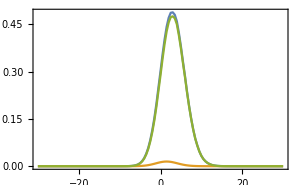

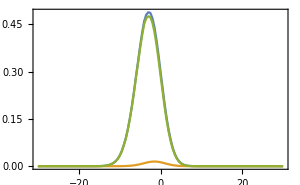

```mathematica
ListLinePlot[A3Density,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
ListLinePlot[A3Density⟦All,-1;;1;;-1⟧,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

### A_3 Morse points 2

```mathematica
Simplify[π(T11-T22)Abs[T1111 (-T1112^2+T1111 (T1122+(2 T122^2)/(T11-T22)))](p[{T11,0,T22,0,0,T122,T1111,T1112, T1122},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{2,2}},τ]]/p[{T22,T122,T1111,T1112,T1122},Cov[{{0,2},{1,2},{4,0},{3,1},{2,2}},τ]]),Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]
```

1/(π τ_3^3 √(-8 τ_3^12+38 τ_2^2 τ_3^8 τ_4^2-55 τ_2^4 τ_3^4 τ_4^4+25 τ_2^6 τ_4^6))4 ⅇ^(-(-256 (5 T1111^2+28 T1112^2-10 T1111 T1122+5 T1122^2) τ_3^18-160 (14 T11 (T1111-T1122)-7 T122^2+10 (-T1111+T1122) T22) τ_3^16 τ_4^2+40 (302 T11 T1111-190 T11 T1122-193 T122^2-170 T1111 T22+90 T1122 T22) τ_2^2 τ_3^12 τ_4^4-100 (212 T11 T1111-60 T11 T1122-191 T122^2-92 T1111 T22+20 T1122 T22) τ_2^4 τ_3^8 τ_4^6+4000 (3 T11 T1111-5 T122^2-T1111 T22) τ_2^6 τ_3^4 τ_4^8+7500 T122^2 τ_2^8 τ_4^10+625 (-3 T11+T22)^2 τ_2^6 τ_3^2 τ_4^10+4 τ_3^14 (16 (105 T1111^2+632 T1112^2-130 T1111 T1122+25 T1122^2) τ_2^2 τ_4^2-5 (7 T11-5 T22)^2 τ_4^4)-5 τ_3^10 (256 (9 T1111^2+56 T1112^2-5 T1111 T1122) τ_2^4 τ_4^4-5 (217 T11^2-246 T11 T22+65 T22^2) τ_2^2 τ_4^6)+50 τ_3^6 (128 (T1111^2+6 T1112^2) τ_2^6 τ_4^6-5 (39 T11^2-34 T11 T22+7 T22^2) τ_2^4 τ_4^8))/(10 τ_3^2 τ_4^2 (7 τ_3^4-15 τ_2^2 τ_4^2) (2 τ_3^4-5 τ_2^2 τ_4^2) (4 τ_3^4-5 τ_2^2 τ_4^2) (τ_3^4-τ_2^2 τ_4^2))) (T11-T22) Abs[T1111 (-T1112^2+T1111 (T1122+(2 T122^2)/(T11-T22)))] √(-70 τ_3^6 τ_4^4+150 τ_2^2 τ_3^2 τ_4^6)

```mathematica
Module[{arg,det,random,randomArg,randomDet},
arg=With[{tmp=Simplify[π(T11-T22)Abs[T1111 (-T1112^2+T1111 (T1122+(2 T122^2)/(T11-T22)))](p[{T11,0,T22,0,0,T122,T1111,T1112, T1122},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{2,2}},τ]]/p[{T22,T122,T1111,T1112,T1122},Cov[{{0,2},{1,2},{4,0},{3,1},{2,2}},τ]]),Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]/.moments},
Compile[{{T11,_Real},{T22,_Real},{T122,_Real},{T1111,_Real},{T1112,_Real},{T1122,_Real}},HeavisideTheta[T11-T22]tmp]];
det=Compile[{{T11,_Real},{T22,_Real},{T122,_Real},{T1111,_Real},{T1112,_Real},{T1122,_Real}},HeavisideTheta[T1111 (-T1112^2+T1111 (T1122+(2 T122^2)/(T11-T22)))]];

random=RandomVariate[MultinormalDistribution[Cov[{{0,2},{1,2},{4,0},{3,1},{2,2}},τ]/.moments],Nsamples];
Monitor[A3Density2=Table[
randomArg=ParallelMap[arg[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random];
randomDet=ParallelMap[det[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random];
{Mean[randomArg],Mean[randomArg randomDet],Mean[randomArg (1-randomDet)]}
,{λ,-range,range,1/2}]ᵀ;,N[λ]];]
Beep[]
```

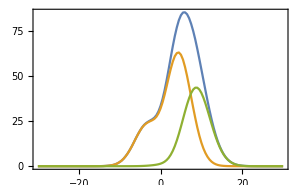

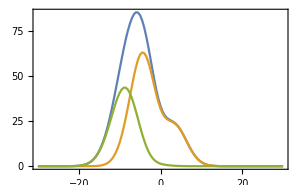

```mathematica
ListLinePlot[A3Density2,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
ListLinePlot[A3Density2⟦All,-1;;1;;-1⟧,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

### A_4 point density

```mathematica
Simplify[π(T11-T22)Abs[(T1112+(3T112 T122)/(T11-T22))(T11111+(T112(15T112 T122 + 10 T1112(T11-T22)))/(T11-T22)^2)](p[{T11,0,T22,0,T112,T122,-(3 T112^2)/(T11-T22),T1112,T11111},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{5,0}},τ]]/p[{T22,T112,T122,T1112,T11111},Cov[{{0,2},{2,1},{1,2},{3,1},{5,0}},τ]]),Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]
```

-((8 ⅇ^((4 T22^2)/(3 τ_2^2)+(2 (T11-5 T22)^2 τ_3^4)/(-34 τ_2^2 τ_3^4+35 τ_2^4 τ_4^2)+64 τ_2^2 ((9 T112^4)/((T11-T22)^2 (34 τ_3^4-35 τ_2^2 τ_4^2))+T1112^2/(4 τ_3^4-5 τ_2^2 τ_4^2))+(1225 T122^2 τ_4^4)/(-125 τ_3^2 τ_4^4+126 τ_3^4 τ_5^2)+252 T122^2 τ_5^2 (5/(125 τ_4^4-126 τ_3^2 τ_5^2)+8/(-25 τ_4^4+252 τ_3^2 τ_5^2))+16 τ_3^2 (-(21 T11 T112^2)/((T11-T22) (34 τ_3^4-35 τ_2^2 τ_4^2))+(3 T112^2 T22)/((T11-T22) (34 τ_3^4-35 τ_2^2 τ_4^2))+(16 T11111^2)/(125 τ_4^4-126 τ_3^2 τ_5^2)+(32 T11111^2)/(-25 τ_4^4+252 τ_3^2 τ_5^2)-(1008 T1112^2 τ_5^2)/(125 τ_4^6-1260 τ_3^2 τ_4^2 τ_5^2))+5 τ_4^2 ((21 T11^2)/(68 τ_3^4-70 τ_2^2 τ_4^2)+(21 T22^2)/(68 τ_3^4-70 τ_2^2 τ_4^2)+(7 T11 T22)/(-34 τ_3^4+35 τ_2^2 τ_4^2)+(64 T1112^2)/(25 τ_4^4-252 τ_3^2 τ_5^2)+32 T11111 T122 (1/(-125 τ_4^4+126 τ_3^2 τ_5^2)+4/(-25 τ_4^4+252 τ_3^2 τ_5^2)))) (-T11+T22) Abs[(T1112+(3 T112 T122)/(T11-T22)) (T11111+(5 T112 (2 T11 T1112+3 T112 T122-2 T1112 T22))/(T11-T22)^2)] τ_4 √(-750 τ_4^4+7560 τ_3^2 τ_5^2))/(π τ_3 √((136 τ_3^8-310 τ_2^2 τ_3^4 τ_4^2+175 τ_2^4 τ_4^4) (-125 τ_4^4+126 τ_3^2 τ_5^2))))

```mathematica
Module[{arg,det,random,randomArg,randomDet},
arg=With[{tmp=Simplify[π(T11-T22)Abs[(T1112+(3T112 T122)/(T11-T22))(T11111+(T112(15T112 T122 + 10 T1112(T11-T22)))/(T11-T22)^2)] p[{T11,0,T22,0,T112,T122,-(3 T112^2)/(T11-T22),T1112,T11111},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{4,0},{3,1},{5,0}},τ]]/p[{T22,T112,T122,T1112,T11111},Cov[{{0,2},{2,1},{1,2},{3,1},{5,0}},τ]],Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]/.moments},
Compile[{{T11,_Real},{T22,_Real},{T112,_Real},{T122,_Real},{T1112,_Real},{T11111,_Real}},HeavisideTheta[T11-T22]tmp]];

random=RandomVariate[MultinormalDistribution[Cov[{{0,2},{2,1},{1,2},{3,1},{5,0}},τ]/.moments],Nsamples];
Monitor[A4Number=Table[
randomArg=ParallelMap[arg[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧]&,random];
Mean[randomArg]
,{λ,-range,range,1/2}];,N[λ]]]
Beep[]
```

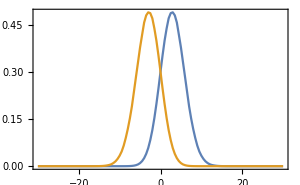

```mathematica
ListLinePlot[{A4Number,A4Number⟦-1;;1;;-1⟧},DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

### D_4 point density

```mathematica
p[{T11,0,T22},Cov[{{2,0},{1,1},{0,2}},τ]]
```

(2 √2 ⅇ^(1/2 (-T11 ((3 T11)/τ_2^2-T22/τ_2^2)-T22 (-T11/τ_2^2+(3 T22)/τ_2^2))))/(π^(3/2) √(τ_2^6))

```mathematica
Simplify[Abs[(T111-T122)T122-(T222-T112)T112] p[{T11,0,T22,T111,T112,T122,T222},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}},τ]]/(p[{T11,0,T22},Cov[{{2,0},{1,1},{0,2}},τ]]p[{T111,T112,T122,T222},Cov[{{3,0},{2,1},{1,2},{0,3}},τ]]),Assumptions->{Subscript[τ, 0]>0,Subscript[τ, 1]>0,Subscript[τ, 2]>0,Subscript[τ, 3]>0,Subscript[τ, 4]>0,Subscript[τ, 5]>0}]
```

Abs[T112^2+(T111-T122) T122-T112 T222]

```mathematica
Module[{arg,det,random,randomArg,randomDet},
arg=Compile[{{T111,_Real},{T112,_Real},{T122,_Real},{T222,_Real}},Abs[(T111-T122)T122-(T222-T112)T112]];
det=Compile[{{T111,_Real},{T112,_Real},{T122,_Real},{T222,_Real}},HeavisideTheta[(T111-T122)T122-(T222-T112)T112]];

random=RandomVariate[MultinormalDistribution[Cov[{{3,0},{2,1},{1,2},{0,3}},τ]/.moments],Nsamples];
randomArg=ParallelMap[arg[#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧]&,random];
randomDet=ParallelMap[det[#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧]&,random];
{m1, m2, m3}={Mean[randomArg],Mean[randomArg randomDet],Mean[randomArg (1-randomDet)]}
]
```

{201.728,100.815,100.913}

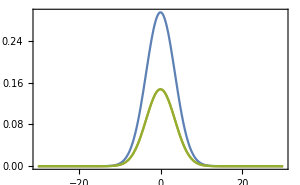

```mathematica
Plot[Evaluate[{m1, m2, m3}p[{λ,0,λ},Cov[{{2,0},{1,1},{0,2}},τ]]/.moments],{λ,-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

## Scale space

```mathematica
Module[{arg,det,random,randomArg,randomDet,R=1},
arg=With[{tmp=π(T11-T22)1/Abs[T1122+(2 T122^2)/(T11-T22)] Abs[-((R (T11 (T11111+T11122) T1122-T11 T1112 (T11112+T11222)+2 (T11111+T11122) T122^2-2 T1112 T122 (T1112+T1222)-(T11111+T11122) T1122 T22+T1112 (T11112+T11222) T22) (T11^3 (3 T1112^2 T11122 T1122-3 T11112 T1112 T1122^2+T11111 T1122^3-T1112^3 T11222)+T11111 (2 T122^2-T1122 T22)^3+3 T11112 T1112 T22 (-2 T122^2+T1122 T22)^2-3 T1112^2 (2 T122^2-T1122 T22) (2 T122^3+2 T1122 T122 T22-T11122 T22^2)+3 T11^2 (T11111 T1122^2 (2 T122^2-T1122 T22)+T11112 T1112 T1122 (-4 T122^2+3 T1122 T22)+T1112^2 (2 T122 (T1122^2+T11122 T122)-3 T11122 T1122 T22)+T1112^3 (-2 T122 T1222+T11222 T22))+T1112^3 T22 (-6 T122 T1222 T22+T11222 T22^2+6 T122^2 T222)-3 T11 (-T11111 T1122 (-2 T122^2+T1122 T22)^2+T1112^2 (-2 T1122 T122^3+4 T122 (T1122^2+T11122 T122) T22-3 T11122 T1122 T22^2)+T11112 T1112 (4 T122^4-8 T1122 T122^2 T22+3 T1122^2 T22^2)+T1112^3 (-4 T122 T1222 T22+T11222 T22^2+2 T122^2 T222))))/((T11-T22)^2 (T11 T1122+2 T122^2-T1122 T22)^2))](p[{T11,0,T22,0,0,T122,T222,(T1112 (T11 T1112-T1112 T22))/(T11 T1122+2 T122^2-T1122 T22),T1112,T1122,T1222,T11111,T11112,T11122,T11222},Cov[{{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3},{4,0},{3,1},{2,2},{1,3},{5,0},{4,1},{3,2},{2,3}},τ]]/p[{T22,T122,T222,T1112,T1122,T1222,T11111,T11112,T11122,T11222},Cov[{{0,2},{1,2},{0,3},{3,1},{2,2},{1,3},{5,0},{4,1},{3,2},{2,3}},τ]])/.moments},
Compile[{{T11,_Real},{T22,_Real},{T122,_Real},{T222,_Real},{T1112,_Real},{T1122,_Real},{T1222,_Real},{T11111,_Real},{T11112,_Real},{T11122,_Real},{T11222,_Real}},HeavisideTheta[T11-T22]tmp]];
det=Compile[{{T11,_Real},{T22,_Real},{T122,_Real},{T222,_Real},{T1112,_Real},{T1122,_Real},{T1222,_Real},{T11111,_Real},{T11112,_Real},{T11122,_Real},{T11222,_Real}},
HeavisideTheta[-((R (T11 (T11111+T11122) T1122-T11 T1112 (T11112+T11222)+2 (T11111+T11122) T122^2-2 T1112 T122 (T1112+T1222)-(T11111+T11122) T1122 T22+T1112 (T11112+T11222) T22) (T11^3 (3 T1112^2 T11122 T1122-3 T11112 T1112 T1122^2+T11111 T1122^3-T1112^3 T11222)+T11111 (2 T122^2-T1122 T22)^3+3 T11112 T1112 T22 (-2 T122^2+T1122 T22)^2-3 T1112^2 (2 T122^2-T1122 T22) (2 T122^3+2 T1122 T122 T22-T11122 T22^2)+3 T11^2 (T11111 T1122^2 (2 T122^2-T1122 T22)+T11112 T1112 T1122 (-4 T122^2+3 T1122 T22)+T1112^2 (2 T122 (T1122^2+T11122 T122)-3 T11122 T1122 T22)+T1112^3 (-2 T122 T1222+T11222 T22))+T1112^3 T22 (-6 T122 T1222 T22+T11222 T22^2+6 T122^2 T222)-3 T11 (-T11111 T1122 (-2 T122^2+T1122 T22)^2+T1112^2 (-2 T1122 T122^3+4 T122 (T1122^2+T11122 T122) T22-3 T11122 T1122 T22^2)+T11112 T1112 (4 T122^4-8 T1122 T122^2 T22+3 T1122^2 T22^2)+T1112^3 (-4 T122 T1222 T22+T11222 T22^2+2 T122^2 T222))))/((T11-T22)^2 (T11 T1122+2 T122^2-T1122 T22)^2))]];

random=RandomVariate[MultinormalDistribution[Cov[{{0,2},{1,2},{0,3},{3,1},{2,2},{1,3},{5,0},{4,1},{3,2},{2,3}},τ]/.moments],Nsamples];
Monitor[SS=Table[
randomArg=ParallelMap[arg[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧,#⟦6⟧,#⟦7⟧,#⟦8⟧,#⟦9⟧,#⟦10⟧]&,random];
randomDet=ParallelMap[det[λ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧,#⟦6⟧,#⟦7⟧,#⟦8⟧,#⟦9⟧,#⟦10⟧]&,random];
{Mean[randomArg],Mean[randomArg randomDet],Mean[randomArg (1-randomDet)]}
,{λ,-range,range,1/2}]ᵀ;,N[λ]]]
Beep[]
```

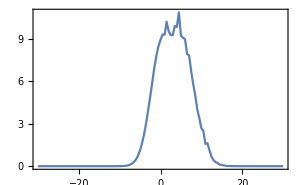

```mathematica
ListLinePlot[SS,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

```mathematica
Simplify[1/Abs[δ22] Abs[-1/δ22^2 R (-3 δ12^2 δ122 δ22+3 δ112 δ12 δ22^2-δ111 δ22^3+δ12^3 δ222) (-(δ111+δ122) δ22+δ12 (δ112+δ222))] p[{δ,δ12^2/δ22,δ12,δ22,δ111,δ112,δ122,δ222},Cov[{{0,0},{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}},σ]]/p[{δ12,δ22,δ111,δ112,δ122,δ222},Cov[{{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}},σ]],Assumptions->{Subscript[σ, 0]>0,Subscript[σ, 1]>0,Subscript[σ, 2]>0,Subscript[σ, 3]>0}]
```

1/(2 π Abs[δ22] √(-σ_1^4+σ_0^2 σ_2^2))√3 ⅇ^(-(2 (-3 δ12^4+6 δ12^2 δ22^2+δ22^4) σ_1^4+6 δ δ22 (δ12^2+δ22^2) σ_1^2 σ_2^2+σ_2^2 ((-3 δ12^2+δ22^2)^2 σ_0^2+3 δ^2 δ22^2 σ_2^2))/(6 δ22^2 σ_2^2 (-σ_1^4+σ_0^2 σ_2^2))) Abs[(R (-δ112 δ12+δ111 δ22+δ122 δ22-δ12 δ222) (3 δ12^2 δ122 δ22-3 δ112 δ12 δ22^2+δ111 δ22^3-δ12^3 δ222))/δ22^2]

```mathematica
Module[{arg,det,random,randomArg,randomDet,R=1},
arg=With[{tmp=Simplify[1/Abs[δ22] Abs[-1/δ22^2 R (-3 δ12^2 δ122 δ22+3 δ112 δ12 δ22^2-δ111 δ22^3+δ12^3 δ222) (-(δ111+δ122) δ22+δ12 (δ112+δ222))] p[{δ,0,0,δ12^2/δ22,δ12,δ22,δ111,δ112,δ122,δ222},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}},σ]]/p[{δ12,δ22,δ111,δ112,δ122,δ222},Cov[{{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}},σ]],Assumptions->{Subscript[σ, 0]>0,Subscript[σ, 1]>0,Subscript[σ, 2]>0,Subscript[σ, 3]>0}]/.moments},
Compile[{{δ,_Real},{δ12,_Real},{δ22,_Real},{δ111,_Real},{δ112,_Real},{δ122,_Real},{δ222,_Real}},tmp]];
det=Compile[{{δ,_Real},{δ12,_Real},{δ22,_Real},{δ111,_Real},{δ112,_Real},{δ122,_Real},{δ222,_Real}},HeavisideTheta[-1/δ22^2 R (-3 δ12^2 δ122 δ22+3 δ112 δ12 δ22^2-δ111 δ22^3+δ12^3 δ222) (-(δ111+δ122) δ22+δ12 (δ112+δ222))]];

random=RandomVariate[MultinormalDistribution[Cov[{{1,1},{0,2},{3,0},{2,1},{1,2},{0,3}},σ]/.moments],Nsamples];
Monitor[δSS=Table[
randomArg=ParallelMap[arg[δ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧,#⟦6⟧]&,random];
randomDet=ParallelMap[det[δ,#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,#⟦5⟧,#⟦6⟧]&,random];
{Mean[randomArg],Mean[randomArg randomDet],Mean[randomArg(1-randomDet)]}
,{δ,-range,range,1/2}]ᵀ;,N[δ]]]
Beep[]
```

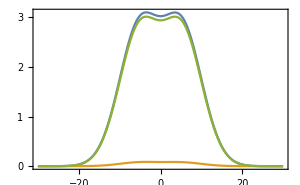

```mathematica
ListLinePlot[δSS,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

```mathematica
Module[{arg,det,random,randomArg,randomDet,R=1},
arg=With[{tmp=Simplify[Abs[-R δ22^2 δ111(δ111+δ122)] p[{δ,0,0,0,0,δ22,δ111,δ122},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{1,2}},σ]]/p[{δ22,δ111,δ122},Cov[{{0,2},{3,0},{1,2}},σ]],Assumptions->{Subscript[σ, 0]>0,Subscript[σ, 1]>0,Subscript[σ, 2]>0,Subscript[σ, 3]>0}]/.moments},
Compile[{{δ,_Real},{δ22,_Real},{δ111,_Real},{δ122,_Real}},HeavisideTheta[-δ22]tmp]];
det=Compile[{{δ,_Real},{δ22,_Real},{δ111,_Real},{δ122,_Real}},HeavisideTheta[-R δ22^2 δ111(δ111+δ122)]];

random=RandomVariate[MultinormalDistribution[Cov[{{0,2},{3,0},{2,1}},σ]/.moments],Nsamples];
Monitor[δSS=Table[
randomArg=ParallelMap[arg[δ,#⟦1⟧,#⟦2⟧,#⟦3⟧]&,random];
randomDet=ParallelMap[det[δ,#⟦1⟧,#⟦2⟧,#⟦3⟧]&,random];
{Mean[randomArg],Mean[randomArg randomDet],Mean[randomArg(1-randomDet)]}
,{δ,-range,range,1/2}]ᵀ;,N[δ]]]
Beep[]
```

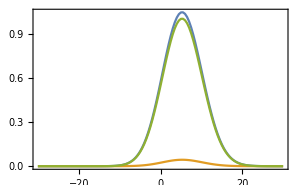

```mathematica
ListLinePlot[δSS,DataRange->{-range,range},Frame->True,ImageSize->300,PlotRange->All]
```

```mathematica
Monitor[Module[{R=1},
test=Table[
Quiet[NIntegrate[Evaluate[Abs[-R δ22^2 δ111(δ111+δ122)]π p[{δ,0,0,0,0,δ22,δ111,δ122},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{1,2}}]]/.moments]
,{δ22,-∞,0},{δ111,-∞,∞},{δ122,-∞,∞}]]
,{δ,-30,30,1/2}];
],N[δ]]
```

```mathematica
Monitor[Module[{R=1},
test2=Table[
Quiet[NIntegrate[Evaluate[Abs[-R δ22^2 δ111(δ111+δ122)]HeavisideTheta[-R δ22^2 δ111(δ111+δ122)]π p[{δ,0,0,0,0,δ22,δ111,δ122},Cov[{{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{1,2}}]]/.moments]
,{δ22,-∞,0},{δ111,-∞,∞},{δ122,-∞,∞}]]
,{δ,-30,30,1/2}];
],N[δ]]
```

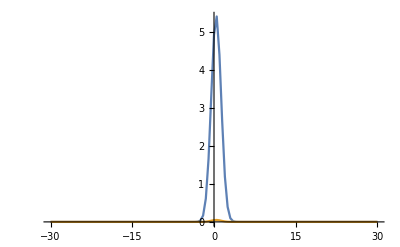

```mathematica
ListLinePlot[{test,test2},DataRange->{-range,range},PlotRange->All]
```